```mathematica
AppendTo[$Path,"C:\\Users\\Nilo\\__DATA\\Mega\\DATA\\eclipse-workspace2\\NumberTheory"];
<<NumberTheory`
```

```mathematica
ComplexAnalysis`BranchPoints[√(z^2-1),z]
ComplexAnalysis`BranchCuts[√(z^2-1),z]
```

{-1,1,ComplexInfinity}

(-1<Re[z]<0&&Im[z]==0)||Re[z]==0||(0<Re[z]<1&&Im[z]==0)

## Topic

### Definition / Theorem

This is text.

#### Example

# Notes CAN

tmp

## temp

### Definition / Theorem

#### Example

Complex Integration

## Contour Integral

### Definition / Theorem

#### Example

```mathematica
cContourIntegral[1/z,z,path[4]]//Expand
```

2 ⅈ π

Visualizations

## Visualize Function

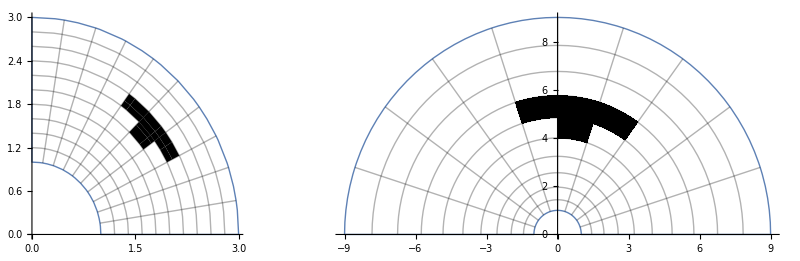

```mathematica
F[z_]:=z^2;
t1=0;
t2=Pi/2;
r1=1;
r2=3;
dt=(t2-t1)/10;
dr=(r2-r1)/10;

GraphicsRow[With[{z=r Exp[I t],col=Black},
ParametricPlot[ReIm@#[z],{r,r1,r2},{t,t1,t2},
Mesh->9,
MeshShading->ArrayPad[{{None,col},{col,col},{None,col}},{{3,4},{5,3}},None],
Frame->False,
AxesOrigin->{0,0}]]&/@{Identity,F}]
```

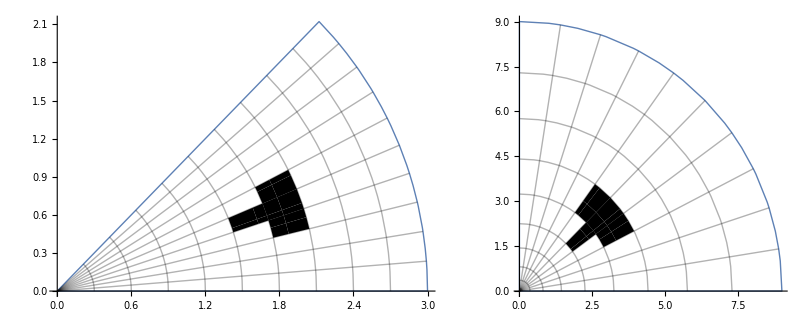

```mathematica
ClearAll[t1,t2,r1,r2,dt,dr]
F[z_]:=z^2;
t1=0;
t2=Pi/4;
r1=0;
r2=3;
GraphicsRow[With[{z=r Exp[I t],col=Black},
ParametricPlot[ReIm@#[z],{r,r1,r2},{t,t1,t2},
Mesh->9,
MeshShading->ArrayPad[{{None,col},{col,col},{None,col}},{{3,4},{5,3}},None],
Frame->False,
AxesOrigin->{0,0}]]&/@{Identity,F}]
```

1

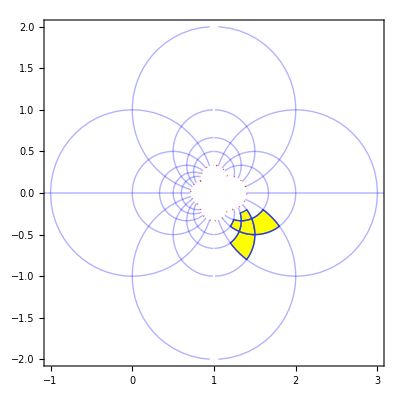

```mathematica
1


Block[{z=x+I y},ParametricPlot[ReIm[(z+1)/(z-1)],{x,-6,6},{y,-6,6},MeshFunctions->Automatic,Mesh->{Range[-4,4],Range[-4,4]},Axes->False,PlotStyle->None,Axes->False,MeshStyle->Blue,BoundaryStyle->Directive[Dotted,Red,Thick],PlotPoints->50]];
Block[{z=x+I y},ParametricPlot[ReIm[(z+1)/(z-1)],{x,#1,#1+1},{y,#2,#2+1},MeshFunctions->Automatic,Mesh->{Range[#1,#1+1],Range[#2,#2+1]},MeshShading->{{None,None},{None,Yellow}},Axes->False,PlotStyle->None,Axes->False,MeshStyle->Blue,PlotPoints->50]&@@@{{2,2},{3,2},{4,2},{3,3},{3,1}}];
Show[%,%%,PlotRange->{{-1,3},{-2,2}}]
```

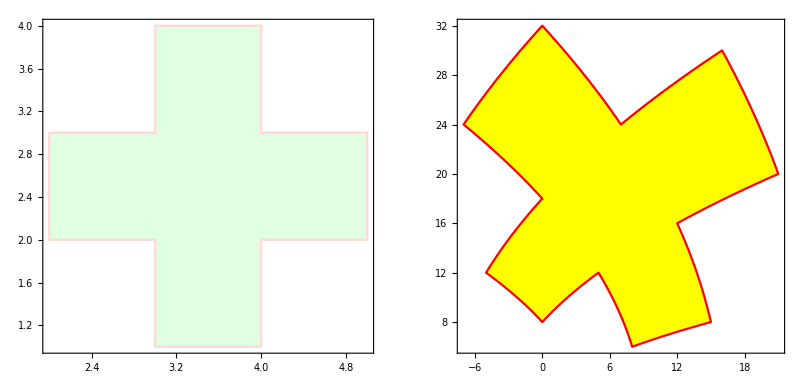

```mathematica
Block[{z=x+I y},RegionPlot[RegionUnion[ParametricRegion[ReIm[z],{{x,#1,#1+1},{y,#2,#2+1}}]&@@@{{2,2},{3,2},{4,2},{3,3},{3,1}}],BoundaryStyle->LightRed,PlotStyle->LightGreen,PlotRange->All]];
Block[{z=x+I y},RegionPlot[RegionUnion[ParametricRegion[ReIm[z^2],{{x,#1,#1+1},{y,#2,#2+1}}]&@@@{{2,2},{3,2},{4,2},{3,3},{3,1}}],BoundaryStyle->Red,PlotStyle->Yellow]];
GraphicsRow[{%%,%}]
```

## Test-0

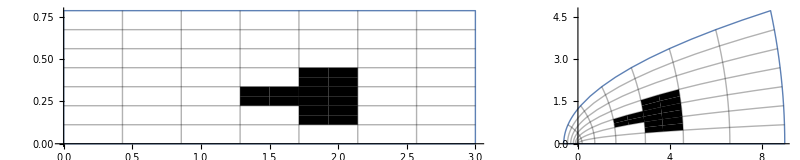

```mathematica
ClearAll[t1,t2,r1,r2,dt,dr]
F[z_]:=z^2;
t1=0;
t2=Pi/4;
r1=0;
r2=3;
GraphicsRow[
With[{z=r + I t,col=Black},
ParametricPlot[ReIm@#[z],{r,r1,r2},{t,t1,t2},
Mesh->6,
MeshShading->ArrayPad[{{None,col},{col,col},{None,col}},{{1,5},{3,5}},None],
Frame->False,
AxesOrigin->{0,0}]]&/@{Identity,F}]
```

## Test-1

```mathematica
f[s_]:=s
GraphicsRow[
With[{s=σ+I t},
ParametricPlot[ReIm@#[s],{x,0,4},{y,0,8}]
]&/@{Identity,f}]
```

-Graphics-

## Test-2

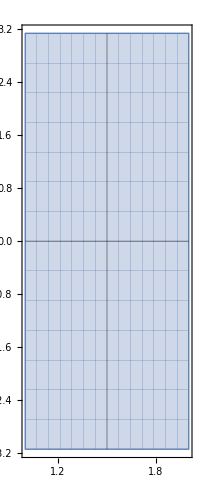

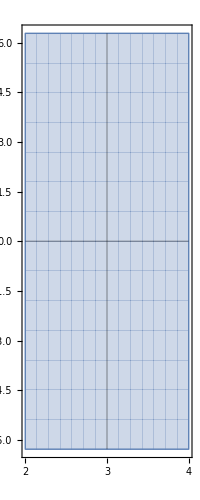

```mathematica
With[{s=σ+I t},
ParametricPlot[ReIm[s],{σ,1,2},{t,-π,π},Mesh->1]
]
With[{s=σ+I t},
ParametricPlot[ReIm[2s],{σ,1,2},{t,-π,π},Mesh->1]
]
```